first, a soliton :

```mathematica
u[x_,t_] = 1/4/Cosh[Sqrt[1/48] (x-40 - 1/12 t )]^2
```

1/4 Sech[(-40-t/12+x)/(4 √3)]^2

```mathematica
D[u[x,t],t] + u[x,t] D[u[x,t],x] + D[u[x,t],{x,3}]
```

(Sech[(-40-t/12+x)/(4 √3)]^2 Tanh[(-40-t/12+x)/(4 √3)])/(96 √3)-(Sech[(-40-t/12+x)/(4 √3)]^4 Tanh[(-40-t/12+x)/(4 √3)])/(32 √3)+1/4 ((Sech[(-40-t/12+x)/(4 √3)]^4 Tanh[(-40-t/12+x)/(4 √3)])/(12 √3)-(Sech[(-40-t/12+x)/(4 √3)]^2 Tanh[(-40-t/12+x)/(4 √3)]^3)/(24 √3))

```mathematica
FullSimplify[%]
```

0

```mathematica
Clear[u]
```

```mathematica
u[x_] = 1/4/Cosh[Sqrt[1/48] (x-40 )]^2
```

1/4 Sech[(-40+x)/(4 √3)]^2

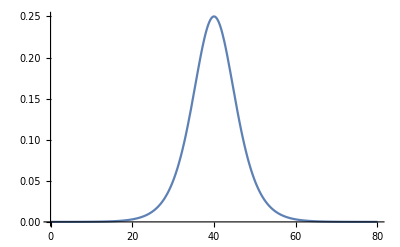

```mathematica
Plot[u[x],{x,0,80}]
```

```mathematica
Clear[c]
```

```mathematica
c[l_][t_] := Conjugate[c[-l][t]] /; l<0;
c[l_][t_] := 0 /; Abs[l]>M;
M=10; L = 80;
eqns = Table[D[c[l][t],t] + (2l I Pi/L)^3 c[l][t] +Sum[ 2 m Pi I/L  c[m][t] c[l-m][t] ,{m,-M,M}]==0,{l,0,M}];
```

```mathematica
initialconds = Table[c[l][0]== 1/L NIntegrate[u[x] Exp[-2 Pi I l x/L],{x,0,L}] ,{l,0,M}]
```

{c[0][0]==0.0433004,c[1][0]==-0.0384468-7.50361×10^-18 ⅈ,c[2][0]==0.0276968+3.66849×10^-18 ⅈ,c[3][0]==-0.0171973-4.98685×10^-18 ⅈ,c[4][0]==0.00970615-7.87758×10^-18 ⅈ,c[5][0]==-0.00515717-6.21512×10^-18 ⅈ,c[6][0]==0.00263182+1.912×10^-17 ⅈ,c[7][0]==-0.00130642+2.62127×10^-18 ⅈ,c[8][0]==0.000634901-3.35188×10^-18 ⅈ,c[9][0]==-0.000304034-1.06645×10^-18 ⅈ,c[10][0]==0.00014355-7.5018×10^-19 ⅈ}

```mathematica
sl=NDSolve[Join[eqns,initialconds],Table[c[l][t],{l,0,M}],{t,0,1600}]
```

{{c[0][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[1][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[2][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[3][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[4][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[5][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[6][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[7][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[8][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[9][t]→InterpolatingFunction[{{0., 1600.}}, <>][t],c[10][t]→InterpolatingFunction[{{0., 1600.}}, <>][t]}}

```mathematica
u[x_,t_] = Sum[c[n][t] Exp[I 2 n Pi x/L],{n,-M,M}]/.%;
```

```mathematica
Table[Plot[u[x,t],{x,0,L},PlotRange->{-1,1},PlotLabel->" M = "<> ToString[M] <>", t = "<>ToString[t]],{t,0,940,20}];
```

```mathematica
ListAnimate[%]
```

two solitons:

```mathematica
Clear["Global`*"]
```

```mathematica
c[l_][t_] := Conjugate[c[-l][t]] /; l<0;
c[l_][t_] := 0 /; Abs[l]>M;
M=12; L = 120; 
eqns = Table[D[c[l][t],t] + (2l I Pi/L)^3 c[l][t]  +Sum[ 2 m Pi I/L  c[m][t] c[l-m][t] ,{m,-M,M}]==0,{l,0,M}];
```

```mathematica
u[x_] = 1/3/Cosh[Sqrt[1/36] (x-30 )]^2 + 1/4 /Cosh[Sqrt[1/48] (x-90 )]^2
```

1/4 Sech[(-90+x)/(4 √3)]^2+1/3 Sech[1/6 (-30+x)]^2

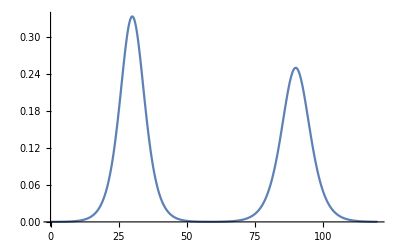

```mathematica
Plot[u[x],{x,0,120}]
```

```mathematica
initialconds = Table[c[l][0]== 1/L NIntegrate[u[x] Exp[-2 Pi I l x/L],{x,0,L}] ,{l,0,M}]
```

{c[0][0]==0.0621943,c[1][0]==-6.32049×10^-6-0.00465473 ⅈ,c[2][0]==-0.0519362+1.17126×10^-6 ⅈ,c[3][0]==-5.09824×10^-6+0.00521976 ⅈ,c[4][0]==0.0322476+1.69648×10^-6 ⅈ,c[5][0]==-3.68087×10^-6-0.00449364 ⅈ,c[6][0]==-0.0167212+1.73735×10^-6 ⅈ,c[7][0]==-2.60011×10^-6+0.00302078 ⅈ,c[8][0]==0.00783601+1.60033×10^-6 ⅈ,c[9][0]==-1.86951×10^-6-0.0017323 ⅈ,c[10][0]==-0.00347051+1.42974×10^-6 ⅈ,c[11][0]==-1.38388×10^-6+0.000904169 ⅈ,c[12][0]==0.00148038+1.27138×10^-6 ⅈ}

```mathematica
NDSolve[Join[eqns,initialconds],Table[c[l][t],{l,0,M}],{t,0,4800},MaxSteps->50000]
```

{{c[0][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[1][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[2][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[3][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[4][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[5][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[6][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[7][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[8][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[9][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[10][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[11][t]→InterpolatingFunction[{{0., 4800.}}, <>][t],c[12][t]→InterpolatingFunction[{{0., 4800.}}, <>][t]}}

```mathematica
u[x_,t_] = Sum[c[n][t] Exp[I 2 n Pi x/L],{n,-M,M}]/.%;
```

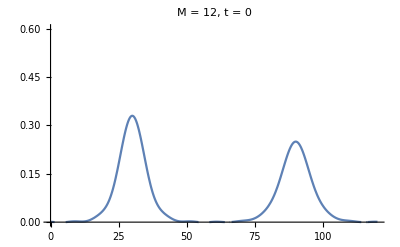
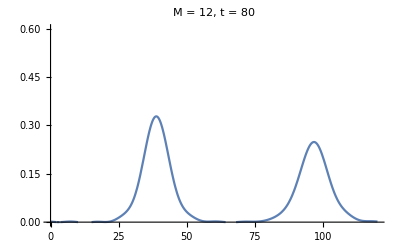
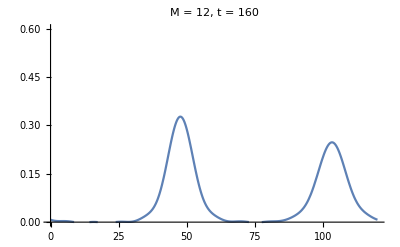
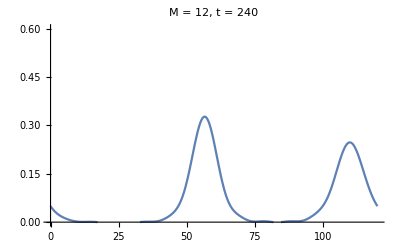
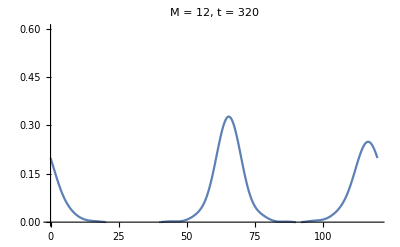
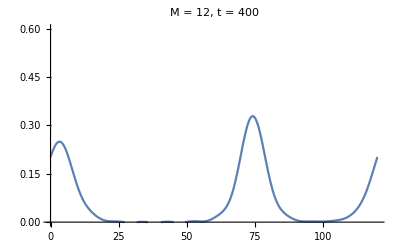
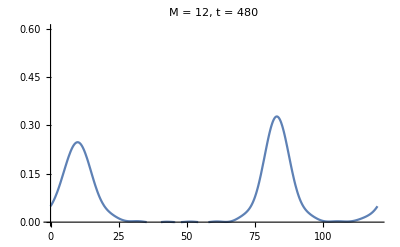
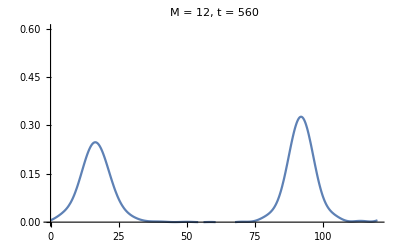

```mathematica
Table[Plot[u[x,t],{x,0,L},PlotRange->{0,.6},PlotLabel->" M = "<> ToString[M] <>", t = "<>ToString[t]],{t,0,4800,80}]
```

```mathematica
ListAnimate[%]
```

single wave : breaking into solitons

```mathematica
Clear["Global`*"]
```

```mathematica
M=12; L = 80; 
c[l_][t_] := Conjugate[c[-l][t]] /; l<0;
c[l_][t_] := 0 /; Abs[l]>M;

eqns = Table[D[c[l][t],t] + (2l I Pi/L)^3 c[l][t]  +Sum[ 2 m Pi I/L  c[m][t] c[l-m][t] ,{m,-M,M}]==0,{l,0,M}];
```

```mathematica
initialconds = Table[c[l][0]== 0 ,{l,0,M}];
initialconds[[2]] = c[1][0]==1/8
```

c[1][0]==1/8

```mathematica
NDSolve[Join[eqns,initialconds],Table[c[l][t],{l,0,M}],{t,0,800}]
```

{{c[0][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[1][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[2][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[3][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[4][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[5][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[6][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[7][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[8][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[9][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[10][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[11][t]→InterpolatingFunction[{{0., 800.}}, <>][t],c[12][t]→InterpolatingFunction[{{0., 800.}}, <>][t]}}

```mathematica
u[x_,t_] = Sum[c[n][t] Exp[I 2 n Pi x/L],{n,-M,M}]/.%;
```

```mathematica
Table[Plot[u[x,t],{x,0,L},PlotRange->{-1,1},PlotLabel->" M = "<> ToString[M] <>", t = "<>ToString[t]],{t,0,800,10}];
```

```mathematica
ListAnimate[%]
```